```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
```

### Pre-homeostasis ODEs

#### Lagrangian formulation

```mathematica
RodOdeLagrangian[R:{__?NumericQ}]:=Block[
{Sol,S,s,nx,ny,x,y,θ,m},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S]*(x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];
{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2
];

EquilSolLagrangian[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,m,nx,ny},{S,0,L/2}][[1]];
```

## Obtain pre-homeostasis solutions

```mathematica
(* Get the data for the initial solution *)
initSolData = Import["~/Documents/MorphoCrypt/Data/planarmorphorodsinextkf0p01L1sol_1"];
y0=initSolData[[300]][[4]];
nx0=initSolData[[300]][[5]];
m0=initSolData[[300]][[8]];
R0 = {nx0, y0, m0};
```

```mathematica
W=Function[s,Exp[-s^2/(.16)^2]];
```

First simulate in the Lagrangian frame for Wnt-based growth.

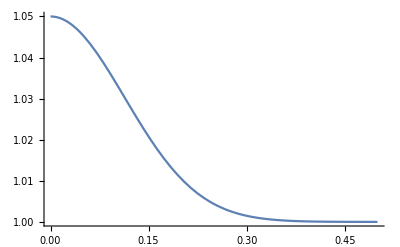

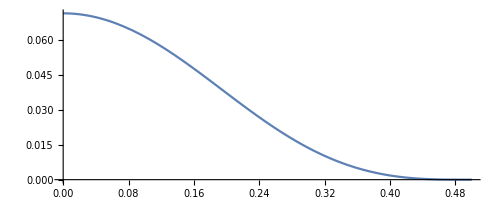

```mathematica
Clear[γ,R,SolLagrangian,solLagrangian,EB,px,py];

(* parameters *)
w = 0.010;
L0=0.125;
h = 0.015;
kf =0.01;
(*Q = 0.1;
n = 2;*)

k=(12*kf*L0^4)/(w*h^3);
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=10;
γ[S_]=1+dt*W[S];
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1;
SolLagrangian=FindRoot[RodOdeLagrangian[R],{R,R0}];
Plot[γ[S],{S,0,1/2}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSolLagrangian[R/.SolLagrangian[[1]]]],{S,0,L/2}]
```

```mathematica
(* first step *)
grs={};
γ[S_]=1+dt*W[S];
SolLagrangian=FindRoot[RodOdeLagrangian[R],{R,R/.SolLagrangian}];
solLagrangian=EquilSolLagrangian[R/.SolLagrangian[[1]]];
rs=R/.SolLagrangian;
AppendTo[grs,{γ[S],L,EB[s],k,rs,solLagrangian,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.solLagrangian,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.solLagrangian,{S,0,L/2}];
```

```mathematica
(* second step *)
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.solLagrangian,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
SolLagrangian=FindRoot[RodOdeLagrangian[R],{R,R/.SolLagrangian}];
solLagrangian=EquilSolLagrangian[R/.SolLagrangian[[1]]];
re=R/.SolLagrangian[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,solLagrangian,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.solLagrangian,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.solLagrangian,{S,0,L/2}];
```

```mathematica
(* Iterate the solution over time now *) 
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.45;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.solLagrangian,{S,0,L/2}]];
P2=Plot[nx[S]/.solLagrangian,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
While[flag==0,
t = (re - rs);
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.solLagrangian,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
SolLagrangian=Quiet[Reap[FindRoot[RodOdeLagrangian[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeLagrangian[R/.SolLagrangian[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
Clear[γ];
γ = γOld;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
solLagrangian=EquilSolLagrangian[R/.SolLagrangian[[1]]];
rs = re;
re = R/.SolLagrangian[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,solLagrangian,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.solLagrangian,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.solLagrangian,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.solLagrangian,{S,0,L/2}]];
P2=Plot[(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]])/.solLagrangian,{S,0,L/2},PlotRange-> {-100, 0}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[SolLagrangian[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.0625

0.03125

0.015625

0.0195313

0.0244141

0.0305176

0.0152588

0.00762939

0.00953674

0.0119209

0.0149012

0.0186265

0.0232831

0.0291038

0.0363798

0.0454747

0.0227374

0.0284217

0.0355271

0.0177636

0.0222045

0.0277556

0.0346945

0.0433681

0.021684

0.010842

0.00542101

0.00271051

0.00338813

0.00169407

0.000847033

0.000423516

0.000529396

0.000661744

0.000330872

0.00041359

0.000206795

0.000103398

0.000129247

0.000161559

0.0000807794

0.0000403897

0.0000201948

0.0000100974

5.04871×10^-6

6.31089×10^-6

3.15544×10^-6

1.57772×10^-6

1.97215×10^-6

9.86076×10^-7

1.2326×10^-6

1.54074×10^-6

1.92593×10^-6

2.40741×10^-6

3.00927×10^-6

3.76158×10^-6

4.70198×10^-6

5.87747×10^-6

7.34684×10^-6

9.18355×10^-6

0.0000114794

0.0000143493

0.0000179366

0.0000224208

0.000028026

0.0000350325

0.0000437906

0.0000547382

0.0000684228

0.0000342114

0.0000171057

8.55285×10^-6

4.27642×10^-6

2.13821×10^-6

1.06911×10^-6

5.34553×10^-7

2.67276×10^-7

1.33638×10^-7

1.67048×10^-7

8.35239×10^-8

4.17619×10^-8

2.0881×10^-8

1.04405×10^-8

1.30506×10^-8

1.63133×10^-8

2.03916×10^-8

1.01958×10^-8

5.09789×10^-9

2.54895×10^-9

1.27447×10^-9

$Aborted

0.00117549

$Aborted

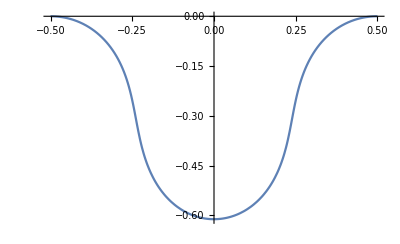

```mathematica
ParametricPlot[{{x[S],-y[S]},{-x[S], -y[S]}}/.solLagrangian,{S, 0, 1/2},PlotRange-> Full]
```

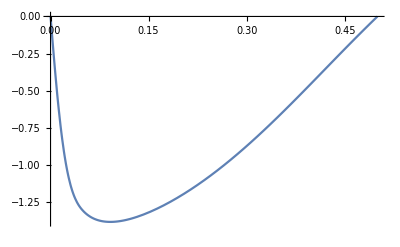

```mathematica
Plot[(θ[S])/.solLagrangian,{S, 0, 0.5},PlotRange-> Full]
```

```mathematica
WntScale=NIntegrate[W[S],{S, 0, 0.5}]
```

0.141795

```mathematica
WntScale=NIntegrate[W[s],{s, 0, l}]
```

Check the homogeneous stress

We need to define the homeostatic shape, (x[s], y[s]), which are defined by θ[s] and subsequently, m=θ’[s].

```mathematica
currentLength=s[0.5]/.solLagrangian
```

0.867207

```mathematica
S0Mesh = Range[0, 0.5, 0.005];
```

```mathematica
xHom=Interpolation[Table[{s[S0Mesh[[i]]],x[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
yHom=Interpolation[Table[{s[S0Mesh[[i]]],y[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
θHom=Interpolation[Table[{s[S0Mesh[[i]]],θ[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
mHom=Interpolation[Table[{s[S0Mesh[[i]]],m[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
```

```mathematica
nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]/.solLagrangian
```

Cos[InterpolatingFunction[{{0., 0.5}}, <>][S]] InterpolatingFunction[{{0., 0.5}}, <>][S]+Sin[InterpolatingFunction[{{0., 0.5}}, <>][S]] InterpolatingFunction[{{0., 0.5}}, <>][S]

```mathematica
h^2/(12*L0^2)
```

0.0012

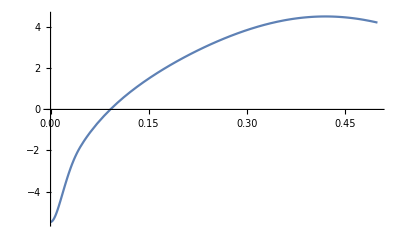

```mathematica
Plot[{m[S]/.solLagrangian},{S, 0, 0.5}]
```

## Homeostasis ODEs

```mathematica
W=Function[s,Exp[-s^2/(.16)^2]];
```

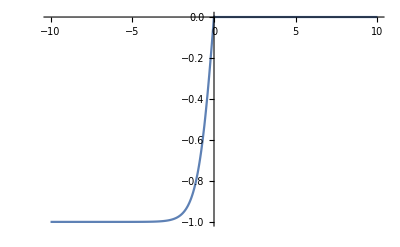

```mathematica
f=Function[m,Tanh[m]*1/2(1+Tanh[-50m])];
Plot[f[ns],{ns,-10,10}]
```

```mathematica
ParametricPlot[{s[S]/.solLagrangian,W[s[S]/.solLagrangian]+0.6*W[s[S]/.solLagrangian]*f[((nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]])/.solLagrangian)+ 25]/.ParSubs},{S, 0, 1/2},PlotRange-> Full]
```

ReplaceAll::reps: {solLagrangian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

```mathematica
nx[0]/.solLagrangian
```

-26.3036

```mathematica
Clear[k];
```

```mathematica
(*ParSubs={k->(12*0.01*125^4)/(10*15^3),μ->0.5,ρ->1,ns->-15,n0->-20};*)
ParSubs={k->2000,μ->0.5,ρ->1,ns->-15,n0->-20};
AppendTo[ParSubs, β->(W[0]+μ*Tanh[(n0-ns)]*W[0])/.ParSubs];
(W[0]+μ*Tanh[(n0-ns)])/.ParSubs
```

0.500045

Obtain the homeostatic morphology.

```mathematica
BuckledSol = Import["~/Documents/MorphoCrypt/Mathematica/Solutions/homeostaticwntbasedsol.csv"];
```

```mathematica
Length[BuckledSol]
```

308

```mathematica
l
```

0.5

```mathematica
sLag = Interpolation[Table[{BuckledSol[[i,1]],BuckledSol[[i,2]]},{i, 1, Length[BuckledSol]}]];
xLag =Interpolation[Table[{BuckledSol[[i,1]],BuckledSol[[i,3]]},{i, 1, Length[BuckledSol]}]];
yLag =Interpolation[Table[{BuckledSol[[i,1]],BuckledSol[[i,4]]},{i, 1, Length[BuckledSol]}]];
θLag =Interpolation[Table[{BuckledSol[[i,1]],BuckledSol[[i,5]]},{i, 1, Length[BuckledSol]}]];
θpLag =Interpolation[Table[{BuckledSol[[i,1]],BuckledSol[[i,6]]},{i, 1, Length[BuckledSol]}]];
```

```mathematica
l = BuckledSol[[Length[BuckledSol], 2]];
xHom =Interpolation[Table[{BuckledSol[[i,2]],BuckledSol[[i,3]]},{i, 1, Length[BuckledSol]}]];
yHom =Interpolation[Table[{BuckledSol[[i,2]],BuckledSol[[i,4]]},{i, 1, Length[BuckledSol]}]];
θHom =Interpolation[Table[{BuckledSol[[i,2]],BuckledSol[[i,5]]},{i, 1, Length[BuckledSol]}]];
θpHom =Interpolation[Table[{BuckledSol[[i,2]],BuckledSol[[i,6]]},{i, 1, Length[BuckledSol]}]];
```

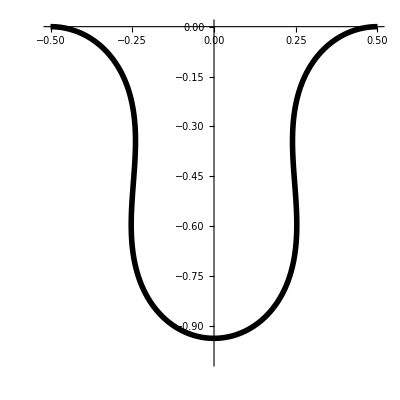

```mathematica
ParametricPlot[{{xHom[s],-yHom[s]},{-xHom[s],-yHom[s]}},{s, 0, l},PlotRange-> {{-0.5, 0.5}, {-1, 0}},PlotStyle-> {{Thickness[0.01],Black},{Thickness[0.01],Black}}]
```

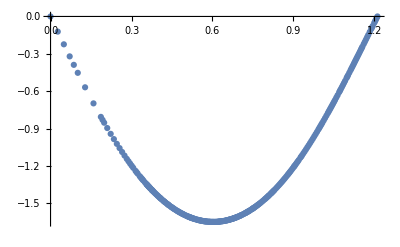

```mathematica
ListPlot[Table[{BuckledSol[[i,1]],BuckledSol[[i,4]]},{i, 1, Length[BuckledSol]}]]
```

```mathematica
ParSubs
```

{k→3000,μ→0.5,ρ→1,ns→-15,n0→-20,β→0.500045}

```mathematica
Plot[D[θHom[s],s],{s, eps, l}]
```

General::ivar: 0.000117714 is not a valid variable.

General::ivar: 0.0178138 is not a valid variable.

General::ivar: 0.0355098 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
eps=0.0001;
Es = 0.0012;
InextensibleHomeostasisSol=NDSolve[{v'[s]==-(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]*W[s]),
nx'[s]==k *(xHom[s]-px[s]),
ny'[s]==k*(yHom[s]-py[s]),
px'[s]==ρ (px[s]-xHom[s])/v[s],
py'[s]==ρ*(py[s]-yHom[s])/v[s],
II'[s]==(β-(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]))/v[s],
Sh'[s]==Exp[-II[s]],
nx[eps]==n0,
ny[eps]==0,
px[eps]==eps*ρ/(ρ+(W[0]+μ*f[n0-ns])),
py[eps]==yHom[eps],
v[eps]==-eps*(W[0]+μ*f[n0-ns]),
II[eps]==0,Sh[eps]==eps}/.ParSubs,{nx, ny, px, py, v,II,Sh},{s, eps, l},MaxStepSize-> 0.005,Method-> "StiffnessSwitching"][[1]];
ExtensibleHomeostasisSol=NDSolve[{v'[s]==(Es*(k *(xHom[s]-px[s])*Cos[θHom[s]]+k*(yHom[s]-py[s])*Sin[θHom[s]]+(θpHom[s])*(ny[s]*Cos[θHom[s]]-nx[s]*Sin[θHom[s]]))*v[s])/(1+Es*(nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]))-(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]*W[s]),
nx'[s]==k *(xHom[s]-px[s]),
ny'[s]==k*(yHom[s]-py[s]),
px'[s]==ρ (px[s]-xHom[s])/v[s],
py'[s]==ρ*(py[s]-yHom[s])/v[s],
II'[s]==(β-(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]))/v[s],
Sh'[s]==Exp[-II[s]],
nx[eps]==n0,
ny[eps]==0,
px[eps]==eps*ρ/(ρ+(W[0]+μ*f[n0-ns])),
py[eps]==yHom[eps],
v[eps]==-eps*(W[0]+μ*f[n0-ns]),
II[eps]==0,Sh[eps]==eps}/.ParSubs,{nx, ny, px, py, v,II,Sh},{s, eps,l},Method-> "StiffnessSwitching"][[1]];
```

```mathematica
Clear[γ,S0]
```

```mathematica
γFun=Function[{s,t},A0 Exp[β t]Exp[II[s]]];
S0Fun=Function[{s,t},Exp[-β t]Sh[s]/A0];
```

We choose the constant so that Lmu = 1/2 at t=0

```mathematica
A0=2*Sh[s]/.ExtensibleHomeostasisSol/.s->l;
```

```mathematica
A0
```

12.0614

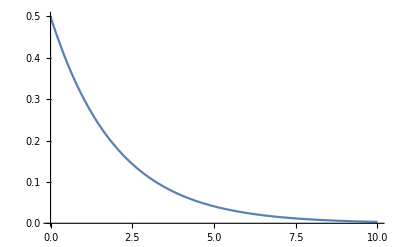

```mathematica
Lmu=Function[t,S0Fun[s,t]/.ExtensibleHomeostasisSol/.ParSubs/.s->l];
Plot[Lmu[t],{t,0,10},PlotRange-> Full]
```

```mathematica
Manipulate[Plot[γFun[s, TT]/.ExtensibleHomeostasisSol/.ParSubs,{s, eps, l}],{TT, 0, 10}]
```

```mathematica
ns/.ParSubs
```

-17.5

```mathematica
nx[eps]/.InextensibleHomeostasisSol
```

{-25.}

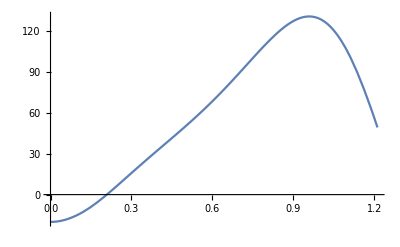

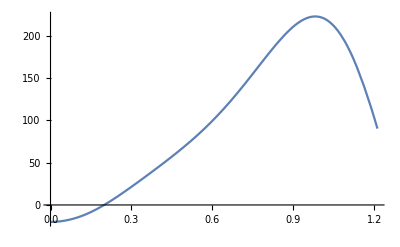

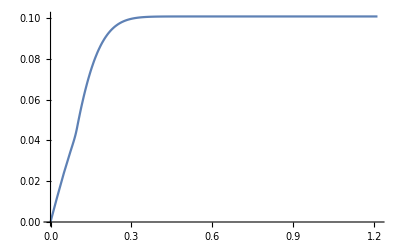

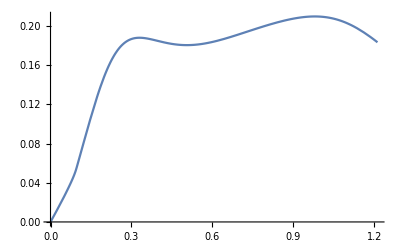

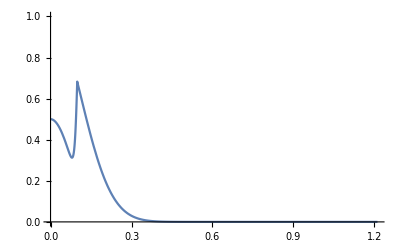

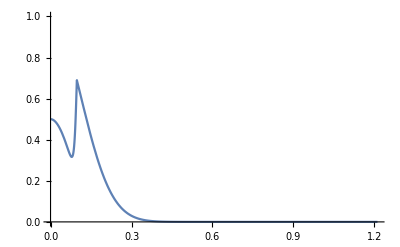

```mathematica
Plot[(nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]])/.InextensibleHomeostasisSol,{s, eps, l}]
Plot[(nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]])/.ExtensibleHomeostasisSol,{s, eps, l}]
Plot[-v[s]/.InextensibleHomeostasisSol,{s, eps, l},PlotRange-> Full]
Plot[-v[s]/.ExtensibleHomeostasisSol,{s, eps, l},PlotRange-> Full]
Plot[ W[s]+μ*f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]/.InextensibleHomeostasisSol/.ParSubs,{s, eps, l},PlotRange-> {0, 1}]
Plot[ W[s]+μ*f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]/.ExtensibleHomeostasisSol/.ParSubs,{s, eps, l},PlotRange-> {0, 1}]
```

Define the various initial profiles, as obtained by the homeostasis equations. We define the solutions at s = 0.

```mathematica
sMesh=Range[eps,l, 30*eps];
Length[sMesh]
```

404

```mathematica
S0Init=Interpolation[Join[{{0, 0}}, Table[{sMesh[[i]],S0Fun[sMesh[[i]],0]/.ExtensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l, 1/2}}]];
γInit=Interpolation[Join[{{0, A0}}, Table[{sMesh[[i]],γFun[sMesh[[i]],0]/.ExtensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,γFun[l,0]/.ExtensibleHomeostasisSol}}]];
pxHom=Interpolation[Join[{{0, 0}}, Table[{sMesh[[i]],px[sMesh[[i]]]/.ExtensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,px[l]/.ExtensibleHomeostasisSol}}]];
pyHom=Interpolation[Join[{{0, yHom[0]}}, Table[{sMesh[[i]],py[sMesh[[i]]]/.ExtensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,py[l]/.ExtensibleHomeostasisSol}}]];
nxHom=Interpolation[Join[{{0, n0/.ParSubs}}, Table[{sMesh[[i]],nx[sMesh[[i]]]/.ExtensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,nx[l]/.ExtensibleHomeostasisSol}}]];
nyHom=Interpolation[Join[{{0, 0}}, Table[{sMesh[[i]],ny[sMesh[[i]]]/.ExtensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,ny[l]/.ExtensibleHomeostasisSol}}]];
mHom = Interpolation[Join[{{0,θpHom[0]/(1+Es*nxHom[0])}},Table[{sMesh[[i]],θpHom[s]/(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))/.s->sMesh[[i]]},{i, 1, Length[sMesh]}],{{l,θpHom[l]/(1+Es*(nxHom[l]*Cos[θHom[l]]+nyHom[l]*Sin[θHom[l]]))}}]];
vHom=Interpolation[Join[{{0, 0}}, Table[{sMesh[[i]],v[sMesh[[i]]]/.ExtensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,v[l]/.ExtensibleHomeostasisSol}}]];
```

```mathematica
ParSubs
```

{k→2000,μ→0.5,ρ→1,ns→-15,n0→-20,β→0.500045}

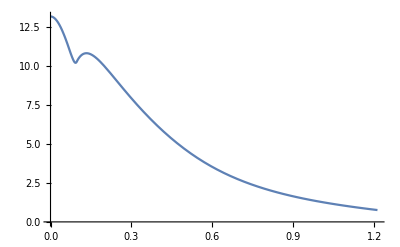

```mathematica
Plot[A0*Exp[II[s]]/.ExtensibleHomeostasisSol/.s-> S,{S, eps, l}]
```

## Stability of solutions

Let’s derive the required stability equations to make sure we’re doing the right thing.

```mathematica
VelocityLaw = v[s,t]-> α[s,t]*γ[s,t]*D[S0[s,t],t];
ExtensibilityLaw = α[s,t]-> 1+ES*(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]);
```

```mathematica
BalanceEqns = {D[S0[s,t],s]-1/(α[s,t]*γ[s,t]),D[x[s,t],s]-Cos[θ[s,t]],D[y[s,t],s]-Sin[θ[s,t]],D[nx[s,t],s]-k*(x[s,t]-px[s,t]),D[ny[s,t],s]-k*(y[s,t]-py[s,t]),D[px[s,t],s]-(D[px[s,t],t]-ρ*(x[s,t]-px[s,t]))/v[s,t],D[py[s,t],s]-(D[py[s,t],t]-ρ*(y[s,t]-py[s,t]))/v[s,t],D[θ[s,t],s]-m[s,t]/α[s,t],D[m[s,t],s]-nx[s,t]*Sin[θ[s,t]]-ny[s,t]*Cos[θ[s,t]],D[γ[s,t],s]-(D[γ[s,t],t]-γ[s,t]*(W0[s]+f[(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]])-ns]))/v[s,t]}/.VelocityLaw/.ExtensibilityLaw;
```

```mathematica
Σh[s]=Function[Sh[s]/A0/.ExtensibleHomeostasisSol];
Γ
```

```mathematica
StabilityPer = {S0[s,t]-> Σh[s]*Exp[-β*t]+ϵ*Σ1[s]*Exp[-β*t]*Exp[ω*t],
γ[s,t]-> Γh[s]*Exp[β*t]+ϵ*Γ1[s]*Exp[β*t]*Exp[ω*t],
x[s,t]-> xh[s]+ϵ*x1[s]*Exp[ω*t],
y[s,t]-> yh[s]+ϵ*y1[s]*Exp[ω*t],
nx[s,t]-> nxh[s]+ϵ*nx1[s]*Exp[ω*t],
ny[s,t]-> nyh[s]+ϵ*ny1[s]*Exp[ω*t],
px[s,t]-> pxh[s]+ϵ*px1[s]*Exp[ω*t],
py[s,t]-> pyh[s]+ϵ*py1[s]*Exp[ω*t],
θ[s,t]-> θh[s]+ϵ*θ1[s]*Exp[ω*t],
m[s,t]-> mh[s]+ϵ*m1[s]*Exp[ω*t]};
StabilityPer = Join[StabilityPer,D[StabilityPer,s],D[StabilityPer,t]];
```

```mathematica
PerturbedEqns =CoefficientList[Normal[Series[(BalanceEqns/.StabilityPer),{ϵ,0,1}]],ϵ]
```

{{-ⅇ^(-t β)/((1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s])+ⅇ^(-t β) Σh'[s],(ⅇ^(-t β+t ω) (Γ1[s]+ES Cos[θh[s]] nxh[s] Γ1[s]+ES nyh[s] Sin[θh[s]] Γ1[s]+ES Cos[θh[s]] nx1[s] Γh[s]+ES ny1[s] Sin[θh[s]] Γh[s]+ES Cos[θh[s]] nyh[s] Γh[s] θ1[s]-ES nxh[s] Sin[θh[s]] Γh[s] θ1[s]))/((1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]])^2 Γh[s]^2)+ⅇ^(-t β+t ω) Σ1'[s]},{-Cos[θh[s]]+xh'[s],ⅇ^(t ω) (Sin[θh[s]] θ1[s]+x1'[s])},{-Sin[θh[s]]+yh'[s],-ⅇ^(t ω) (Cos[θh[s]] θ1[s]-y1'[s])},{k pxh[s]-k xh[s]+nxh'[s],ⅇ^(t ω) (k px1[s]-k x1[s]+nx1'[s])},{k pyh[s]-k yh[s]+nyh'[s],ⅇ^(t ω) (k py1[s]-k y1[s]+ny1'[s])},{(ρ pxh[s]-ρ xh[s])/(β (1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s] Σh[s])+pxh'[s],-(ⅇ^(t ω) (β-ω) (ρ pxh[s]-ρ xh[s]) Σ1[s])/(β^2 (1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s] Σh[s]^2)+1/(β Σh[s])ⅇ^(t β) (-(ⅇ^(-t β+t ω) (ρ pxh[s]-ρ xh[s]) Γ1[s])/((1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s]^2)+(ⅇ^(-t β) ((ⅇ^(t ω) (ρ px1[s]+ω px1[s]-ρ x1[s]))/(1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]])-(ⅇ^(t ω) ES (ρ pxh[s]-ρ xh[s]) (Cos[θh[s]] nx1[s]+ny1[s] Sin[θh[s]]+Cos[θh[s]] nyh[s] θ1[s]-nxh[s] Sin[θh[s]] θ1[s]))/(1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]])^2))/Γh[s])+ⅇ^(t ω) px1'[s]},{(ρ pyh[s]-ρ yh[s])/(β (1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s] Σh[s])+pyh'[s],-(ⅇ^(t ω) (β-ω) (ρ pyh[s]-ρ yh[s]) Σ1[s])/(β^2 (1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s] Σh[s]^2)+1/(β Σh[s])ⅇ^(t β) (-(ⅇ^(-t β+t ω) (ρ pyh[s]-ρ yh[s]) Γ1[s])/((1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s]^2)+(ⅇ^(-t β) ((ⅇ^(t ω) (ρ py1[s]+ω py1[s]-ρ y1[s]))/(1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]])-(ⅇ^(t ω) ES (ρ pyh[s]-ρ yh[s]) (Cos[θh[s]] nx1[s]+ny1[s] Sin[θh[s]]+Cos[θh[s]] nyh[s] θ1[s]-nxh[s] Sin[θh[s]] θ1[s]))/(1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]])^2))/Γh[s])+ⅇ^(t ω) py1'[s]},{-mh[s]/(1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]])+θh'[s],-(ⅇ^(t ω) m1[s])/(1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]])+(ⅇ^(t ω) ES mh[s] (Cos[θh[s]] nx1[s]+ny1[s] Sin[θh[s]]+Cos[θh[s]] nyh[s] θ1[s]-nxh[s] Sin[θh[s]] θ1[s]))/(1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]])^2+ⅇ^(t ω) θ1'[s]},{-Cos[θh[s]] nyh[s]-nxh[s] Sin[θh[s]]+mh'[s],-ⅇ^(t ω) (Cos[θh[s]] ny1[s]+nx1[s] Sin[θh[s]]+Cos[θh[s]] nxh[s] θ1[s]-nyh[s] Sin[θh[s]] θ1[s]-m1'[s])},{(ⅇ^(t β) β Γh[s]-ⅇ^(t β) (-1/2 (1+Tanh[50 ns-50 Cos[θh[s]] nxh[s]-50 nyh[s] Sin[θh[s]]]) Tanh[ns-Cos[θh[s]] nxh[s]-nyh[s] Sin[θh[s]]]+W0[s]) Γh[s])/(β (1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s] Σh[s])+ⅇ^(t β) Γh'[s],-((ⅇ^(t ω) (β-ω) (ⅇ^(t β) β Γh[s]-ⅇ^(t β) (-1/2 (1+Tanh[50 ns-50 Cos[θh[s]] nxh[s]-50 nyh[s] Sin[θh[s]]]) Tanh[ns-Cos[θh[s]] nxh[s]-nyh[s] Sin[θh[s]]]+W0[s]) Γh[s]) Σ1[s])/(β^2 (1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s] Σh[s]^2))+1/(β Σh[s])ⅇ^(t β) ((ⅇ^(t β) β Γh[s]-ⅇ^(t β) (-1/2 (1+Tanh[50 ns-50 Cos[θh[s]] nxh[s]-50 nyh[s] Sin[θh[s]]]) Tanh[ns-Cos[θh[s]] nxh[s]-nyh[s] Sin[θh[s]]]+W0[s]) Γh[s]) (-(ⅇ^(-t β+t ω) Γ1[s])/((1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s]^2)-(ⅇ^(-t β+t ω) ES (Cos[θh[s]] nx1[s]+ny1[s] Sin[θh[s]]+Cos[θh[s]] nyh[s] θ1[s]-nxh[s] Sin[θh[s]] θ1[s]))/((1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]])^2 Γh[s]))+(ⅇ^(-t β) (ⅇ^(t β+t ω) (β+ω) Γ1[s]-ⅇ^(t β+t ω) (-1/2 (1+Tanh[50 ns-50 Cos[θh[s]] nxh[s]-50 nyh[s] Sin[θh[s]]]) Tanh[ns-Cos[θh[s]] nxh[s]-nyh[s] Sin[θh[s]]]+W0[s]) Γ1[s]-1/2 ⅇ^(t β) Γh[s] (-50 ⅇ^(t ω) (-1+Tanh[50 ns-50 Cos[θh[s]] nxh[s]-50 nyh[s] Sin[θh[s]]]^2) Tanh[ns-Cos[θh[s]] nxh[s]-nyh[s] Sin[θh[s]]] (Cos[θh[s]] nx1[s]+ny1[s] Sin[θh[s]]+Cos[θh[s]] nyh[s] θ1[s]-nxh[s] Sin[θh[s]] θ1[s])-ⅇ^(t ω) (1+Tanh[50 ns-50 Cos[θh[s]] nxh[s]-50 nyh[s] Sin[θh[s]]]) (-1+Tanh[ns-Cos[θh[s]] nxh[s]-nyh[s] Sin[θh[s]]]^2) (Cos[θh[s]] nx1[s]+ny1[s] Sin[θh[s]]+Cos[θh[s]] nyh[s] θ1[s]-nxh[s] Sin[θh[s]] θ1[s]))))/((1+ES Cos[θh[s]] nxh[s]+ES nyh[s] Sin[θh[s]]) Γh[s]))+ⅇ^(t β+t ω) Γ1'[s]}}

```mathematica
Clear[Γh,Σh]
```

```mathematica
S0Fun
```

Function[{s,t},(Exp[-β t] Sh[s])/A0]

```mathematica
ΣHom=Function[s,Sh[s]/A0/.ExtensibleHomeostasisSol];
ΓHom=Function[s,A0*Exp[II[s]]/.ExtensibleHomeostasisSol];
```

```mathematica
StabilityMatrix[ω_?NumericQ]:=Block[{sol,s,omegaMatrix},

sol=NDSolve[{Σ1'[s]==-(Γ1[s]+Es Cos[θHom[s]] nxHom[s] Γ1[s]+Es nyHom[s] Sin[θHom[s]] Γ1[s]+Es Cos[θHom[s]] nx1[s] ΓHom[s]+Es ny1[s] Sin[θHom[s]] ΓHom[s]+Cos[θHom[s]] nyHom[s] ΓHom[s] θ1[s]-Es nxHom[s] Sin[θHom[s]] ΣHom[s] θ1[s])/((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])^2 ΓHom[s]^2) ,
x1'[s]==-Sin[θHom[s]] θ1[s],
y1'[s]== Cos[θHom[s]] θ1[s],
nx1'[s]==k*(x1[s]- px1[s]),
ny1'[s]==k*(y1[s]- py1[s]),
px1'[s]==-(ρ (-β+ω) (pxHom[s]-xHom[s]) Σ1[s])/(β^2 (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s] ΣHom[s]^2)-(-ρ (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) (pxHom[s]-xHom[s]) Γ1[s]+ΓHom[s] ((1+Es  Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ((ρ+ω) px1[s]-ρ x1[s])-Es ρ (pxHom[s]-xHom[s]) (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+(Cos[θHom[s]] nyHom[s]-nxHom[s] Sin[θHom[s]]) θ1[s])))/(β (1+Es Cos[θHom[s]] nxHom[s]+Es  nyHom[s] Sin[θHom[s]])^2 ΓHom[s]^2 ΣHom[s]),
py1'[s]==-(ρ (-β+ω) (pyHom[s]-yHom[s]) Σ1[s])/(β^2 (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s] ΣHom[s]^2)-(-ρ (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) (pyHom[s]-yHom[s]) Γ1[s]+ΓHom[s] ((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ((ρ+ω) py1[s]-ρ y1[s])-Es ρ (pyHom[s]-yHom[s]) (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+(Cos[θHom[s]] nyHom[s]-nxHom[s] Sin[θHom[s]]) θ1[s])))/(β (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])^2 ΓHom[s]^2 ΣHom[s]),
θ1'[s]==- (-m1[s] (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])+Es mHom[s] (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+Cos[θHom[s]] nyHom[s] θ1[s]-nxHom[s] Sin[θHom[s]] θ1[s]))/(1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])^2,
m1'[s]== Cos[θHom[s]] ny1[s]+nx1[s] Sin[θHom[s]]+Cos[θHom[s]] nxHom[s] θ1[s]-nyHom[s] Sin[θHom[s]] θ1[s],
Γ1'[s]==+(( (β-ω) (β ΓHom[s]- (-1/2 (1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]) Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]]+W[s]) ΓHom[s]) Σ1[s])/(β^2 (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s] ΣHom[s]^2))-1/(β ΣHom[s]) (( β ΓHom[s]- (-1/2 (1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]) Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]]+W[s]) ΓHom[s]) (-Γ1[s]/((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s]^2)-( Es (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+Cos[θHom[s]] nyHom[s] θ1[s]-nxHom[s] Sin[θHom[s]] θ1[s]))/((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])^2 ΓHom[s]))+( ( (β+ω) Γ1[s]- (-1/2 (1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]) Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]]+W[s]) Γ1[s]-1/2  ΓHom[s] (-50 (-1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]^2) Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]] (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+Cos[θHom[s]] nyHom[s] θ1[s]-nxHom[s] Sin[θHom[s]] θ1[s])-(1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]) (-1+Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]]^2) (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+Cos[θHom[s]] nyHom[s] θ1[s]-nxHom[s] Sin[θHom[s]] θ1[s]))))/((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s])),

Σ1[eps]==0,x1[eps]==0,y1[eps]==1,nx1[eps]==0,ny1[eps]==0,θ1[eps]==0,px1[eps]==0,py1[eps]==0,m1[eps]==0,Γ1[eps]==0,
Σ1'[s]==-(Γ1[s]+Es Cos[θHom[s]] nxHom[s] Γ1[s]+Es nyHom[s] Sin[θHom[s]] Γ1[s]+Es Cos[θHom[s]] nx1[s] ΓHom[s]+Es ny1[s] Sin[θHom[s]] ΓHom[s]+Cos[θHom[s]] nyHom[s] ΓHom[s] θ1[s]-Es nxHom[s] Sin[θHom[s]] ΣHom[s] θ1[s])/((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])^2 ΓHom[s]^2) ,
x1'[s]==-Sin[θHom[s]] θ1[s],
y1'[s]== Cos[θHom[s]] θ1[s],
nx1'[s]==k*(x1[s]- px1[s]),
ny1'[s]==k*(y1[s]- py1[s]),
px1'[s]==-(ρ (-β+ω) (pxHom[s]-xHom[s]) Σ1[s])/(β^2 (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s] ΣHom[s]^2)-(-ρ (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) (pxHom[s]-xHom[s]) Γ1[s]+ΓHom[s] ((1+Es  Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ((ρ+ω) px1[s]-ρ x1[s])-Es ρ (pxHom[s]-xHom[s]) (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+(Cos[θHom[s]] nyHom[s]-nxHom[s] Sin[θHom[s]]) θ1[s])))/(β (1+Es Cos[θHom[s]] nxHom[s]+Es  nyHom[s] Sin[θHom[s]])^2 ΓHom[s]^2 ΣHom[s]),
py1'[s]==-(ρ (-β+ω) (pyHom[s]-yHom[s]) Σ1[s])/(β^2 (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s] ΣHom[s]^2)-(-ρ (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) (pyHom[s]-yHom[s]) Γ1[s]+ΓHom[s] ((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ((ρ+ω) py1[s]-ρ y1[s])-Es ρ (pyHom[s]-yHom[s]) (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+(Cos[θHom[s]] nyHom[s]-nxHom[s] Sin[θHom[s]]) θ1[s])))/(β (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])^2 ΓHom[s]^2 ΣHom[s]),
θ1'[s]==- (-m1[s] (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])+Es mHom[s] (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+Cos[θHom[s]] nyHom[s] θ1[s]-nxHom[s] Sin[θHom[s]] θ1[s]))/(1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])^2,
m1'[s]== Cos[θHom[s]] ny1[s]+nx1[s] Sin[θHom[s]]+Cos[θHom[s]] nxHom[s] θ1[s]-nyHom[s] Sin[θHom[s]] θ1[s],
Γ1'[s]==+(( (β-ω) (β ΓHom[s]- (-1/2 (1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]) Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]]+W[s]) ΓHom[s]) Σ1[s])/(β^2 (1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s] ΣHom[s]^2))-1/(β ΣHom[s]) (( β ΓHom[s]- (-1/2 (1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]) Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]]+W[s]) ΓHom[s]) (-Γ1[s]/((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s]^2)-( Es (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+Cos[θHom[s]] nyHom[s] θ1[s]-nxHom[s] Sin[θHom[s]] θ1[s]))/((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]])^2 ΓHom[s]))+( ( (β+ω) Γ1[s]- (-1/2 (1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]) Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]]+W[s]) Γ1[s]-1/2  ΓHom[s] (-50 (-1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]^2) Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]] (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+Cos[θHom[s]] nyHom[s] θ1[s]-nxHom[s] Sin[θHom[s]] θ1[s])-(1+Tanh[50 ns-50 Cos[θHom[s]] nxHom[s]-50 nyHom[s] Sin[θHom[s]]]) (-1+Tanh[ns-Cos[θHom[s]] nxHom[s]-nyHom[s] Sin[θHom[s]]]^2) (Cos[θHom[s]] nx1[s]+ny1[s] Sin[θHom[s]]+Cos[θHom[s]] nyHom[s] θ1[s]-nxHom[s] Sin[θHom[s]] θ1[s]))))/((1+Es Cos[θHom[s]] nxHom[s]+Es nyHom[s] Sin[θHom[s]]) ΓHom[s])),

Σ2[eps]==0,x2[eps]==0,y2[eps]==0,nx2[eps]==1,ny2[eps]==0,θ2[eps]==0,px2[eps]==0,py2[eps]==0,m2[eps]==0,Γ2[eps]==0
}/.ExtensibleHomeostasisSol/.ParSubs,{Σ1,x1,y1,nx1,ny1,px1,py1,θ1,m1,Γ1[s],x2[s],y2[s],nx2[s],ny2[s],px2[s],py2[s],θ2[s],m2[s],v2[s],G2[s],x3[s],y3[s],nx3[s],ny3[s],px3[s],py3[s],θ3[s],m3[s],v3[s],G3[s]},{s,eps,l},Method->"StiffnessSwitching",MaxSteps-> 10^6];
omegaMatrix ={{x1[s],x2[s],x3[s]},{y1[s],y2[s],y3[s]}, {θ1[s],θ2[s],θ3[s]}}/.sol[[1]]/.s-> l;
Det[omegaMatrix]
];
```

```mathematica
StabilityMatrix[10.0]
```

-1449.76

```mathematica
FindRoot[StabilityMatrix[ω],{,ω,0.1}]
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

```mathematica
StabilityMatrix[-10.0]
```

6.01603×10^200

```mathematica
StabilityMatrix[-5.0]
```

-1.5941×10^78

```mathematica
StabilityMatrix[5.0]
```

-1073.09

```mathematica
StabilityMatrix[2.5]
```

-686.969

```mathematica
Range[0,5]
```

{0,1,2,3,4,5}

```mathematica
Range[0, 50, 10]
```

{0,10,20,30,40,50}

```mathematica
Table[StabilityMatrix[Range[0, 50, 10][[i]]],{i, 1,6}]
```

{-83.5054,-1449.76,-1748.89,-1877.47,-1949.11,-1994.81}

```mathematica
StabilityMatrix[10.0]
```

-1449.76

```mathematica
Plot[10^-2*StabilityMatrix[ω],{ω,-5, 5},PlotPoints-> 10,PlotRange-> {-1, 1}]
```

$Aborted

```mathematica
?ToMatrixSystem
```

ToMatrixSystem[eqn,{},depvars,x] takes a list of differential equations in the dependent variables depvars and independent variable x and puts the equations into linear matrix form dy/dx = A.y
ToMatrixSystem[eqn,bcs,depvars,{x,x0,x1}] also includes the boundary conditions evaluated at x=x0 and x=x1.
ToMatrixSystem[{eqns1,eqns2},{bcs,interfaceEqns},depvars,{x,x0,xmatch,x1}] sets up the function with an interface at x=xmatch, with eqns1 in x0<x<xmatch and eqns2 in xmatch<x<x1.

```mathematica
?Evans
```

Evans[k,sys] evaluates the Evans function from the Compound Matrix Method with potential eigenvalue k, for the system defined from ToMatrixSystem.
Evans[k,A,B,C,{x,x0,x1}] evaluates the Evans function from the Compound Matrix Method with k. Here the linear matrix ODE is given by dy/dx=A.y, with B.y=0 at x=x0 and C.y=0 at x=x1.
For either case a complex number is returned, zeroes of this function correspond to zeroes of the original eigenvalue equation.
Evans[k,{A1,A2},B,C,{F,G},{x,x0,xmatch,x1}] evaluates the Evans function for potential eigenvalue k for an interface problem.
Here there are two linear matrix ODE is given on the left by dy/dx=A1.y, B.y=0 at x=x0, dz/dx=A2.z, and C.z=0 at x=x1, and the interface conditions are given by
F.y + G.z = 0 at the interface given by x=xmatch.

```mathematica
{Sh1'[s]==-((Es*(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]])))/((1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))^2*(A0*Exp[II[s]]))+G1[s]/((1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))*(A0*Exp[II[s]])^2)),
x1'[s]==-θ1[s]*Sin[θHom[s]],
y1'[s]==θ1[s]*Cos[θHom[s]],
nx1'[s]==k*(x1[s]-px1[s]),
ny1'[s]==k*(y1[s]-py1[s]),
px1'[s]==((ω+ρ)*px1[s]-ρ*x1[s])/vHom[s]+(ρ*(xHom[s]-pxHom[s])*v1[s])/(vHom[s])^2,
py1'[s]==((ω+ρ)*py1[s]-ρ*y1[s])/vHom[s]+(ρ*(yHom[s]-pyHom[s])*v1[s])/(vHom[s])^2,
θ1'[s]==m1[s]/(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))-(mHom[s]*Es*(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]])))/(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))^2,m1'[s]==nx1[s]*Sin[θHom[s]]-ny1[s]*Sin[θHom[s]]+θ1[s]*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]),v1'[s]==(D[(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])),s]*v1[s])/(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))+(vHom[s]*Es*(k*(x1[s]-px1[s])*Cos[θHom[s]]-nx1[s]*Sin[θHom[s]]*θHom'[s]+k*(y1[s]-py1[s])*Sin[θHom[s]]+ny1[s]*Cos[θHom[s]]θHom'[s]+θ1[s]*(nyHom'[s]*Cos[θHom[s]]-nyHom[s]*Sin[θHom[s]]*θHom'[s]-nxHom'[s]*Sin[θHom[s]]-nxHom[s]*Cos[θHom[s]]*θHom'[s])+(m1[s]/(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))-(mHom[s]*Es*(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]])))/(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))^2)*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]])))/(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))-((D[1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]),s]*vHom[s]+ω*(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])))*Es*(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]])))/(1+Es*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]]))^2-1/2 (-(-50(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]]))+50 (nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]])) Tanh[50 ns-50*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])]^2) Tanh[ns-(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])]-(1+Tanh[50 ns-50*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])]) (-(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]]))+(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]])) Tanh[ns-(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])]^2)) ,G1'[s]==1/vHom[s]((β+ω-(W[s]+μ*f[(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])-ns]))*G1[s]-(D[A0*Exp[II[s]],s])*v1[s]-(A0*Exp[II[s]])*(1/2 (-(-50(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]]))+50 (nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]])) Tanh[50 ns-50*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])]^2) Tanh[ns-(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])]-(1+Tanh[50 ns-50*(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])]) (-(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]]))+(nx1[s]*Cos[θHom[s]]+ny1[s]*Sin[θHom[s]]+θ1[s]*(nyHom[s]*Cos[θHom[s]]-nxHom[s]*Sin[θHom[s]])) Tanh[ns-(nxHom[s]*Cos[θHom[s]]+nyHom[s]*Sin[θHom[s]])]^2)))),
Sh1[eps]==0,x1[eps]==0,y1[eps]==1,nx1[eps]==0,ny1[eps]==0,θ1[eps]==0,px1[eps]==0,py1[eps]==eps*k,m1[eps]==0,v1[eps]==0,G1[eps]==0,
```

## Validating the homeostatic solutions

```mathematica
FullInextensibleHomeostasis2DSol = NDSolve[{D[S0[s, t],s]==1/γ[s,t],
D[x[s,t],s]==Cos[θ[s,t]],
D[y[s,t],s]==Sin[θ[s,t]],
D[nx[s, t], s]==k*(x[s,t]-px[s, t]),
D[ny[s, t], s]==k*(y[s,t]-py[s, t]),
D[θ[s,t],s]==m[s,t],
D[m[s,t],s]== nx[s,t]*Sin[θ[s,t]]-ny[s,t]*Cos[θ[s,t]],
D[γ[s,t],t]==γ[s,t]*(W[s]*(1+μ*1/2 Tanh[nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns]*(1+Tanh[-50 *(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns)])))+γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[px[s, t], t]==ρ*(x[s,t]-px[s, t])+γ[s,t]*D[px[s,t], s]*D[S0[s, t], t],
D[py[s, t], t]==ρ*(y[s,t]-py[s, t])+γ[s,t]*D[py[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[l,t]==Lmu[t],x[0, t]==0, x[l,t]==0.5, y[l,t]==0,ny[0,t]==0, θ[0, t]==0, θ[l,t]==0,γ[s,0]==γInit[s],S0[s,0]==S0Init[s],x[s,0]==xHom[s],y[s,0]==yHom[s], nx[s,0]==nxHom[s],ny[s,0]==nyHom[s],px[s, 0]==pxHom[s],py[s,0]==pyHom[s],θ[s,0]==θHom[s],m[s,0]==mHom[s]}/.ParSubs,{S0,γ,x,y,nx,ny, px,py,θ,m},{s,0,l},{t,0,1},Method->{"IndexReduction"->Automatic}]
```

```mathematica
FullExtensibleHomeostasis2DSol = NDSolve[{D[S0[s, t],s]==1/((1+Es*(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]))*γ[s,t]),
D[x[s,t],s]==Cos[θ[s,t]],
D[y[s,t],s]==Sin[θ[s,t]],
D[nx[s, t], s]==k*(x[s,t]-px[s, t]),
D[ny[s, t], s]==k*(y[s,t]-py[s, t]),
D[θ[s,t],s]==m[s,t]/(1+Es*(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]])),
D[m[s,t],s]== nx[s,t]*Sin[θ[s,t]]-ny[s,t]*Cos[θ[s,t]],
D[γ[s,t],t]==γ[s,t]*(W[s]*(1+μ*1/2 Tanh[nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns]*(1+Tanh[-50 *(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns)])))+(1+Es*(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]))*γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[px[s, t], t]==ρ*(x[s,t]-px[s, t])+(1+Es*(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]))*γ[s,t]*D[px[s,t], s]*D[S0[s, t], t],
D[py[s, t], t]==ρ*(y[s,t]-py[s, t])+(1+Es*(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]))*γ[s,t]*D[py[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[l,t]==Lmu[t],x[0, t]==0, x[l,t]==0.5, y[l,t]==0,ny[0,t]==0, θ[0, t]==0, θ[l,t]==0,γ[s,0]==γInit[s],S0[s,0]==S0Init[s],x[s,0]==xHom[s],y[s,0]==yHom[s], nx[s,0]==nxHom[s],ny[s,0]==nyHom[s],px[s, 0]==pxHom[s],py[s,0]==pyHom[s],θ[s,0]==θHom[s],m[s,0]==mHom[s]}/.ParSubs,{S0,γ,x,y,nx,ny, px,py,θ,m},{s,0,l},{t,0,1},Method->{"IndexReduction"->Automatic}]
```

{}

```mathematica
S0Init
```

InterpolatingFunction[{{0., 1.2113}}, <>]

```mathematica
sVals = Join[{0.0}, sMesh, {l}];
γLag = Interpolation[Table[{S0Init[sVals[[i]]],γInit[sVals[[i]]]},{i, 1, Length[sVals]}]];
pxLag = Interpolation[Table[{S0Init[sVals[[i]]],pxHom[sVals[[i]]]},{i, 1, Length[sVals]}]];
pyLag = Interpolation[Table[{S0Init[sVals[[i]]],pyHom[sVals[[i]]]},{i, 1, Length[sVals]}]];
```

```mathematica
pxLag[0]
```

2.23414×10^-6

```mathematica
py[0]/.ExtensibleHomeostasisSol
```

0.93682

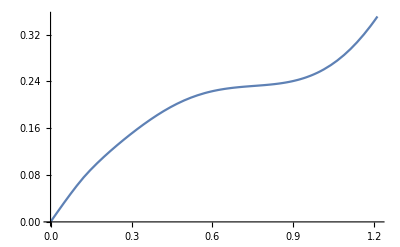

```mathematica
Plot[px[s]/.ExtensibleHomeostasisSol,{s, 0, l}]
```

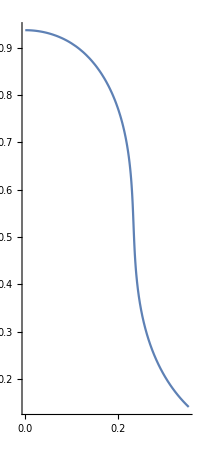

```mathematica
ParametricPlot[{pxLag[S],pyLag[S]},{S, 0, 1/2},PlotRange-> Full]
```

```mathematica
L=Lmu[0];
```

```mathematica
ParSubs
```

{k→1000,μ→0.5,ρ→1,ns→-15,n0→-20,β→0.500045}

```mathematica
mHom[0]
```

-688.873

1000

```mathematica
Eulerian2DSol =  NDSolve[{D[s[S],S]==(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S],
D[x[S],S]==(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S]*Cos[θ[S]],
D[y[S],S]==(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S]*Sin[θ[S]],
D[nx[S], S]==k*(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S]*(x[S]-pxLag[S]),
D[ny[S], S]==k*(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S]*(y[S]-pyLag[S]),
D[θ[S],S]==γLag[S]*m[S],
D[m[S],S]==(nx[S]*Sin[θ[S]]-ny[S]*Cos[θ[S]]),
s[0]==0,x[0]==0,ny[0]==0, θ[0]==0,y[0]==yHom[0], nx[0]==nxHom[0],m[0]==mHom[0]}/.ParSubs,{s,x,y,nx,ny, θ,m},{S, 0, L}]
```

```mathematica
Lagrangian2DSol =  NDSolve[{D[s[S],S]==(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S],
D[x[S],S]==(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S]*Cos[θ[S]],
D[y[S],S]==(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S]*Sin[θ[S]],
D[nx[S], S]==k*(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S]*(x[S]-pxLag[S]),
D[ny[S], S]==k*(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*γLag[S]*(y[S]-pyLag[S]),
D[θ[S],S]==γLag[S]*m[S],
D[m[S],S]==γLag[S]*(1+Es*(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]))*(nx[S]*Sin[θ[S]]-ny[S]*Cos[θ[S]]),
s[0]==0,x[0]==0,ny[0]==0, θ[0]==0,y[0]==yHom[0], nx[0]==nxHom[0],m[0]==mHom[0]}/.ParSubs,{s,x,y,nx,ny, θ,m},{S, 0, L},Method-> "StiffnessSwitching"]
```

{{s→InterpolatingFunction[{{0., 0.5}}, <>],x→InterpolatingFunction[{{0., 0.5}}, <>],y→InterpolatingFunction[{{0., 0.5}}, <>],nx→InterpolatingFunction[{{0., 0.5}}, <>],ny→InterpolatingFunction[{{0., 0.5}}, <>],θ→InterpolatingFunction[{{0., 0.5}}, <>],m→InterpolatingFunction[{{0., 0.5}}, <>]}}

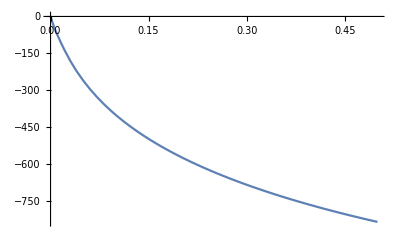

```mathematica
Plot[θ[S]/.Lagrangian2DSol,{S, 0, 0.5}]
```

```mathematica
FullExtensibleHomeostasis2DSol
```

{}⟦1⟧

```mathematica
Manipulate[Plot[nx[s,TT]/.FullExtensibleHomeostasis2DSol,{s, 0, l}],{TT,0, 3}]
```

ReplaceAll::reps: {FullExtensibleHomeostasis2DSol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
(*FullInextensibleHomeostasis2DSol = NDSolve[{D[S0[s, t],s]==1/γ[s,t],
D[x[s,t],s]==Cos[θ[s,t]],
D[y[s,t],s]==Sin[θ[s,t]],
D[nx[s, t], s]==k*(x[s,t]-px[s, t]),
D[ny[s, t], s]==k*(y[s,t]-py[s, t]),
D[θ[s,t],s]==m[s,t],
D[m[s,t],s]== nx[s,t]*Sin[θ[s,t]]-ny[s,t]*Cos[θ[s,t]],
D[γ[s,t],t]==γ[s,t]*(W[s]+μ*1/2 Tanh[nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns]*(1+Tanh[-50 *(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns)]))+γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[px[s, t], t]==ρ*(x[s,t]-px[s, t])+γ[s,t]*D[px[s,t], s]*D[S0[s, t], t],
D[py[s, t], t]==ρ*(y[s,t]-py[s, t])+γ[s,t]*D[py[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[currentLength,t]==Lmu[t],x[0, t]==0, x[currentLength,t]==0.5, y[currentLength,t]==0,ny[0,t]==0, θ[0, t]==0, θ[currentLength,t]==0,γ[s,0]==γInit[s],S0[s,0]==S0Init[s],x[s,0]==xHom[s],y[s,0]==yHom[s], nx[s,0]==nxHom[s],ny[s,0]==nyHom[s],px[s, 0]==pxHom[s],py[s,0]==pyHom[s],θ[s,0]==θHom[s],m[s,0]==mHom[s]}/.ParSubs,{S0,γ,x,y,nx,ny, px,py,θ,m},{s,0,currentLength},{t,0,1},Method->{"IndexReduction"->Automatic}][[1]];*)
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::nlnum1: The function value 0.961045934943242`  - 1.` TagBox[InterpolatingFunction[{{0.`, 0.8959206840006635`}}, {4, 7, 0, {600}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, 2, « 46 », 49, « 551 »}, {0.961045934943242`, 0.961045934943242`, 0.9610407545917243`, 0.9610253921927595`, 0.9609999709745142`, 0.9609646972497743`, 0.9609198631520341`, 0.9608658456939252`, 0.9608031120672956`, « 33 », 0.9676917221589266`, 0.969235685929116`, 0.9709945118695097`, 0.9729927909041419`, 0.9752558657921666`, 0.9778132188720178`, 0.9806973094468253`, 0.9839416379928356`, « 550 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][s]« 49 »« 200 » is not a list of numbers with dimensions {250} when the arguments are {0., « 19 », {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}}.

NDSolve::nlnum1: The function value {Hold[{{-5.35717, -5.29835, -5.12452, -4.84295, -4.46537, -4.00669, -3.48312, -2.91013, -2.30112, -1.66705, -1.01717, -0.359734, 0.297605, 0.947319, 1.58044, 2.18622, 2.75163, 3.2612, 3.69779, 4.04382, 4.28326, 4.40377, 4.39868, 4.26814, 4.01902} + {5.35717, « 23 », -« 18 »}, « 9 »}, {« 1 »}]} is not a list of numbers with dimensions {1} when the arguments are {0., « 19 », {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}}.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Part::partw: Part 1 of {} does not exist.

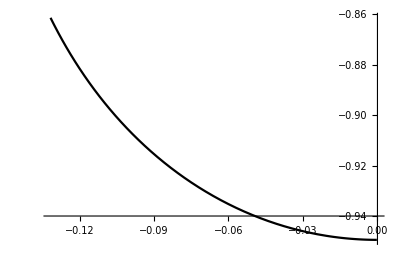

```mathematica
ParametricPlot[{-x[S],-y[S]}/.solLagrangian,{S,eps, LLmu},PlotStyle->Black]
```

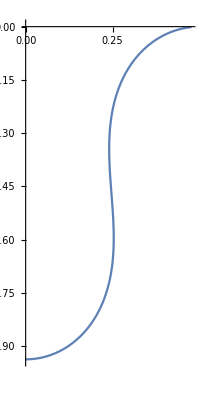

```mathematica
ParametricPlot[{xHom[s],-yHom[s]},{s, 0, l}]
```

```mathematica
SS0=Range[.1,.4,.1];
ss0 = Range[.1,.4,.1];
TT=Range[0.1,10,.1];
(*TT = 0.1;*)
Plots={};
Colors={Blue,Green,Yellow,Red};
For[j=1,j≤Length[TT],j++,
tt=TT[[j]]; (* the time *)
LLmu=Lmu[t]/.ExtensibleHomeostasisSol/.ParSubs/.t->tt;
ss={};
xs={};
ys={};
For[i=1,i≤Length[SS0],i++,
If[LLmu>SS0[[i]],
sSol=FindRoot[SS0[[i]]-(S0[s,t]/.ExtensibleHomeostasisSol/.ParSubs/.t->tt),{s,0.2,eps,1}][[1]];
AppendTo[ss, s/.sSol];
AppendTo[xs,xHom[s/.sSol]];
AppendTo[ys,yHom[s/.sSol]];,
];];]
```

```mathematica
xs
```

{}

```mathematica
ss0
```

{0.01,0.06,0.11,0.16}

```mathematica
SS0=Range[0.01, 0.07, 0.02];
ss0 = Range[0.01, 0.07,.02];
TT=Range[0.0,10.0,0.1];
(*TT = 0.1;*)
Plots={};
Colors = {{193,213,238}, {149,185,79}, {239,207,99}, {212,81,19}}/255;
(*Colors = {{174,191,199},{237,203,106}, {237,142,114},{100,128,105}}/255;*)
For[j=1,j≤ Length[TT],j++,
tt=TT[[j]]; (* the time *)
LLmu=Lmu[t]/.ExtensibleHomeostasisSol/.ParSubs/.t->tt;
ss={};
xs={};
ys={};
ppx={};
ppy = {};
For[i=1,i≤Length[SS0],i++,
If[LLmu>SS0[[i]],
sSol=FindRoot[SS0[[i]]-(S0Fun[s,t]/.ExtensibleHomeostasisSol/.ParSubs/.t->tt),{s,0.2,eps,l}][[1]];
AppendTo[ss, s/.sSol];
AppendTo[xs,xHom[s/.sSol]];
AppendTo[ys,yHom[s/.sSol]];
AppendTo[ppx,pxHom[s/.sSol]];
AppendTo[ppy,pyHom[s/.sSol]];,
];
(*Print[ys]*)];
(* foundation *)

AppendTo[Plots,Show[
(* initial configuration - past Lmu is dashed *)
ParametricPlot[{-xLag[S],-yLag[S]},{S,0,1/2},PlotStyle->Black,PlotRange->{{-0.5, 2},{-1.1,.1}},BaseStyle-> {FontFamily-> "CMU Serif", FontSize-> 18},Epilog-> {Text[Style["Lagrangian", 24], {0.0, 0.2}], Text[Style["Eulerian", 24], {1.5, 0.2}]},AxesOrigin-> {-0.5, 0}],
ParametricPlot[{xLag[S],-yLag[S]},{S,0,1/2},PlotStyle->Black,PlotRange->{{-0.5, 2},{-1.1,.1}}],
(*ParametricPlot[{xLag[S],-yLag[S]},{S,LLmu,1/2},PlotStyle->{Black,Dashed},PlotRange->{{-0.5, 2},{-1.1,.1}}],
ParametricPlot[{-xLag[S],-yLag[S]},{S,LLmu,1/2},PlotStyle->{Black,Dashed},PlotRange->{{-0.5, 2},{-1.1,.1}}],*)
(* and a small disk at Lmu *)
(*Graphics[{Black,Disk[{xLag[LLmu],-yLag[LLmu]},0.01]}],
Graphics[{Black,Disk[{-xLag[LLmu],-yLag[LLmu]},0.01]}],*)(*
Table[Graphics[{Colors[[k]],Disk[{x[SS0[[k]]],-y[SS0[[k]]]}/.solLagrangian,0.04]}],{k,1,Length[SS0]}],
Table[Graphics[{Colors[[k]],Disk[{-x[SS0[[k]]],-y[SS0[[k]]]}/.solLagrangian,0.04]}],{k,1,Length[SS0]}],*)
Table[Graphics[{RGBColor[Colors[[k]]],Disk[{xHom[ss[[k]]] ,-yHom[ss[[k]]]},0.04]}],{k,1,Length[ss]}],
Table[Graphics[{RGBColor[Colors[[k]]],Disk[{-xHom[ss[[k]]] ,-yHom[ss[[k]]]},0.04]}],{k,1,Length[ss]}],

(* the current values *)
ParametricPlot[{{xHom[s] + 1.5,-yHom[s]},{-xHom[s] + 1.5,-yHom[s]}},{s,0,l},PlotStyle-> Black,PlotRange->{{-0.5, 2},{-1.1,.1}},FrameTicksStyle->Directive[Opacity-> 0]],
Table[Graphics[{RGBColor[Colors[[k]]],Disk[{xHom[sLag[SS0[[k]]]]+1.5 ,-yHom[sLag[SS0[[k]]]]},0.04]}],{k,1,Length[ss0]}],
Table[Graphics[{RGBColor[Colors[[k]]],Disk[{-xHom[sLag[SS0[[k]]]] +1.5,-yHom[sLag[SS0[[k]]]]},0.04]}],{k,1,Length[ss0]}],

(* Label the different views *)


(* foundation *)
(*ParametricPlot[{{pxHom[s],-pyHom[s]-0.25},{-pxHom[s],-pyHom[s]-0.25}},{s,0,l},PlotStyle-> Black],
Table[Graphics[{RGBColor[Colors[[k]]],Disk[{ppx[[k]],-ppy[[k]]-0.25},0.04]}],{k,1,Length[ss]}],
Table[Graphics[{RGBColor[Colors[[k]]],Disk[{-ppx[[k]],-ppy[[k]]-0.25},0.04]}],{k,1,Length[ss]}],
(* the connecting spring *)
Table[Graphics[{RGBColor[Colors[[k]]],Dashed,Thick,Line[{{ppx[[k]],-ppy[[k]]-0.25},{xs[[k]],-ys[[k]]}}]}],{k,1,Length[ss]}],
Table[Graphics[{RGBColor[Colors[[k]]],Dashed,Thick,Line[{{-ppx[[k]],-ppy[[k]]-0.25},{-xs[[k]],-ys[[k]]}}]}],{k,1,Length[ss]}],*)
AspectRatio->Automatic,PlotRange->{{-0.5, 2},{-1.1,.3}}]]];
```

```mathematica
TT[[10]]
```

0.9

```mathematica
Manipulate[Show[Plots[[i]],PlotRange-> {-1.3, 0.3}],{i,1, Length[Plots],1}]
```

Part::partd: Part specification Plots ⟦ 46 ⟧ is longer than depth of object.

Show::gtype: Part is not a type of graphics.

Part::partd: Part specification Plots ⟦ 46 ⟧ is longer than depth of object.

Show::gtype: Part is not a type of graphics.

```mathematica
Manipulate[Plot[S0Fun[s,TT]/.ExtensibleHomeostasisSol/.ParSubs,{s, 0, l},PlotRange-> {0, 0.5}],{TT, 0, 3}]
```

InterpolatingFunction::dmval: Input value {0.0000247451} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Export["~/Documents/MorphoCrypt/Mathematica/LagrangianVsEulerian2DCrypt.avi", Table[Plots[[i]],{i,1, Length[Plots]}],ImageSize-> {1000, 625}]
```

~/Documents/MorphoCrypt/Mathematica/LagrangianVsEulerian2DCrypt.avi

```mathematica
1000/1.6
```

625.